```mathematica
datos="/home/amaro/datos10/";
ϕ={0.,0.04027683,0.08055366,0.12083049,0.16110732,0.20138414,0.24166097,0.2819378,0.32221463,0.36249146,0.40276829,0.44304512,0.48332195,0.52359878,0.5638756,0.60415243,0.64442926,0.68470609,0.72498292,0.76525975,0.80553658,0.84581341,0.88609024,0.92636706,0.96664389,1.00692072,1.04719755,1.08747438,1.12775121,1.16802804,1.20830487,1.2485817,1.28885852,1.32913535,1.36941218,1.40968901,1.44996584,1.49024267,1.5305195,1.57079633};
trazas=Table[Import[datos<>"rho"<>ToString[i]<>".dat","Table"],{i,1,12}];
eldichoso=Table[Flatten[Table[Log[10,Abs[trazas[[k]][[i]]]^2],{i,1,40}]],{k,1,12}];
(*graficas=Table[ListLinePlot[Table[{ϕ[[i]],eldichoso[[k]][[i]]},{i,1,40}],Filling->False,PlotLegends->{ToString[k]},PlotStyle->k],{k,1,3}];
Show[graficas,PlotRange->All]*)
```

```mathematica
ListLinePlot[Table[{ϕ[[i]],eldichoso[[1]][[i]]},{i,1,10}],Filling->False,PlotLegends->{ToString[1]}]
```

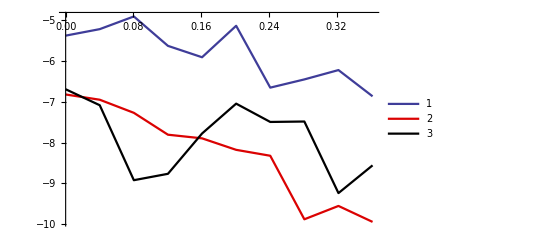

```mathematica
graficas=Table[ListLinePlot[Table[{ϕ[[i]],eldichoso[[k]][[i]]},{i,1,10}],Filling->False,PlotLegends->{ToString[k]},PlotStyle->k],{k,1,3}];
Show[graficas,PlotRange->All]
```

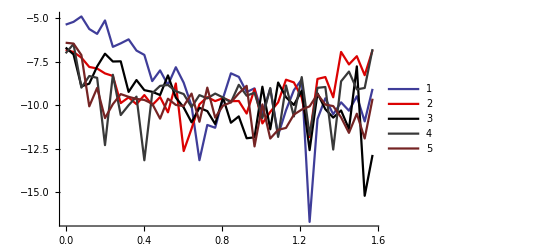

```mathematica
traz=Table[Import[datos<>"ro"<>ToString[i]<>".dat","Table"],{i,1,12}];
eldichoso=Table[Flatten[Table[Log[10,Abs[traz[[k]][[i]]]^2],{i,1,40}]],{k,1,12}];
graficas=Table[ListLinePlot[Table[{ϕ[[i]],eldichoso[[k]][[i]]},{i,1,40}],Filling->False,PlotLegends->{ToString[k]},PlotStyle->k],{k,1,5}];
Show[graficas,PlotRange->All,PlotRegion->]
```

```mathematica
eldichoso[[1]]
```

{-15.0056,-14.846,-14.5348,-15.2567,-15.5362,-14.7639,-16.2821,-16.0804,-15.851,-16.495,-16.745,-18.2511,-17.6356,-18.471,-17.4531,-18.3427,-19.672,-22.7968,-20.7712,-20.9329,-19.2267,-17.8028,-18.0065,-18.8815,-18.6656,-20.1468,-18.6802,-21.3509,-19.9275,-18.7732,-18.1521,-26.3437,-20.4345,-19.2369,-20.1569,-19.4701,-19.9511,-19.1214,-20.5679,-18.6963}

```mathematica
eldichoso[[1]]//Reverse
```

{-18.6963,-20.5679,-19.1214,-19.9511,-19.4701,-20.1569,-19.2369,-20.4345,-26.3437,-18.1521,-18.7732,-19.9275,-21.3509,-18.6802,-20.1468,-18.6656,-18.8815,-18.0065,-17.8028,-19.2267,-20.9329,-20.7712,-22.7968,-19.672,-18.3427,-17.4531,-18.471,-17.6356,-18.2511,-16.745,-16.495,-15.851,-16.0804,-16.2821,-14.7639,-15.5362,-15.2567,-14.5348,-14.846,-15.0056}

```mathematica
Log[10
```